# Pivotal journal

## All journal count

```mathematica
ISSNvspubgenTly=Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/ISSNvspubgenTly.wl"];
```

```mathematica
ISSNvspubgenTly//Length
```

15

```mathematica
Map[Length,ISSNvspubgenTly]
```

{1801,2180,2714,4040,5280,7422,9875,11784,13748,15590,18277,20442,25957,31210,35253}

```mathematica
(ISSNvspubgenTlyEf=Map[Cases[#,{{_},_}]&,ISSNvspubgenTly])//Length
```

15

```mathematica
totaljournalcount=Map[Length,ISSNvspubgenTlyEf]
```

{1800,2179,2713,4039,5279,7421,9874,11783,13747,15589,18276,20441,25956,31209,35252}

## Pivotal journal

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/top1PcISSN.save"];
(* PMIDtoISSN.nbより *)
```

## 主要雑誌数累積

```mathematica
(top1pcISSN=Map[Flatten,Map[#[[1]]&,top1percISSNTallyBygenSort,{2}]])//Length
```

15

```mathematica
pivotaljournalcount=Map[Length,top1pcISSN]
```

{5,11,19,16,14,18,20,17,12,13,19,28,83,136,145}

## 新規出現主要雑誌累積

```mathematica
(top1pcISSNacm=Map[Flatten,FoldList[List,top1pcISSN]])//Length
```

15

```mathematica
(top1pcISSNnewcomer=Prepend[Table[Complement[top1pcISSNacm[[n+1]],top1pcISSNacm[[n]]],{n,1,14}],top1pcISSN[[1]]])//Length
```

15

```mathematica
top1pcISSNnewcomercount=Map[Length,top1pcISSNnewcomer]
```

{5,7,9,4,2,4,3,5,0,2,1,3,54,56,35}

## plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{pivotaljournalcount,top1pcISSNnewcomercount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要雑誌数","新規出現主要雑誌数"}]
```

-Graphics-

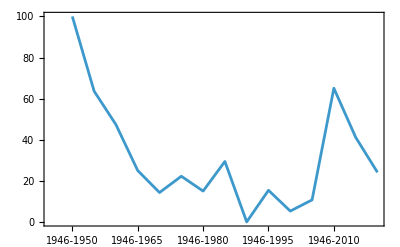
-Graphics-新規出現雑誌の主要雑誌に占める割合（%）

```mathematica
Labeled[ListPlot[top1pcISSNnewcomercount/pivotaljournalcount*100,Joined->True,
Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現雑誌の主要雑誌に占める割合（%）"]
```

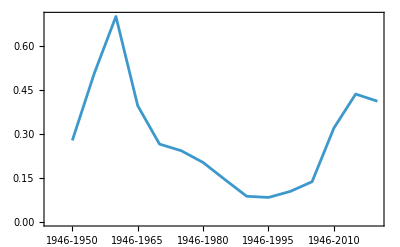
-Graphics-主要雑誌の全雑誌に占める割合（%）

```mathematica
Labeled[ListPlot[pivotaljournalcount/totaljournalcount*100,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要雑誌の全雑誌に占める割合（%）"]
```

## 主要雑誌タイトル

ISSN vs. journal title
ISSNvsTitle.save

ISSNから雑誌タイトルを引くルール：

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal-title/ISSNvsTitle.save"];
```

< 主要雑誌ISSN一覧 >

```mathematica
pivotalJournalISSN=Cases[top1percISSNTallyBygenSort,_String,Infinity]//Union
```

{0001-6322,0001-690X,0002-8614,0002-9297,0002-9572,0003-2697,0003-2700,0003-276X,0003-4819,0003-4932,0003-9861,0003-990X,0004-3591,0005-3678,0006-291X,0006-2952,0006-2960,0006-341X,0006-3525,0007-0920,0007-1021,0007-9235,0009-9147,0010-4809,0012-0472,0012-186X,0014-2956,0014-4827,0016-6731,0018-4888,0019-2791,0020-5915,0021-8898,0021-9193,0021-9258,0021-9525,0021-9681,0021-9738,0022-1007,0022-1295,0022-1465,0022-1554,0022-1759,0022-1767,0022-2836,0022-2844,0022-3050,0022-3514,0022-3751,0022-3956,0022-5320,0025-7079,0027-8424,0027-8874,0028-0836,0028-3878,0028-3932,0028-4793,0031-6768,0031-6997,0032-0889,0033-2909,0033-8419,0036-8075,0042-6822,0066-4154,0076-6879,0077-8923,0085-591X,0090-3493,0092-8674,0095-1137,0095-9898,0095-9901,0096-9621,0098-7484,0099-2240,0108-7673,0140-6736,0146-0749,0147-006X,0149-5992,0160-6689,0161-8105,0162-3257,0163-1829,0165-0270,0165-1781,0168-8510,0168-9525,0169-1015,0173-0835,0192-8651,0195-9131,0197-2456,0261-4189,0263-7855,0264-6021,0266-7061,0270-7306,0271-6801,0277-6715,0305-1048,0366-0753,0366-0826,0378-1119,0512-3054,0586-7614,0737-4038,0740-3194,0749-503X,0884-8734,0888-7543,0903-1936,0907-4449,0925-2738,0950-1991,0952-0481,0959-8138,0960-7412,0962-1083,1046-2023,1049-7323,1053-8119,1058-8388,1061-4036,1063-5157,1064-3745,1065-9471,1076-836X,1079-5006,1079-7114,1088-9051,1095-9203,1096-987X,1097-0215,1097-4164,1097-4172,1098-5336,1176-9343,1353-4505,1362-4962,1367-4803,1367-4811,1399-0047,1465-3249,1465-4644,1465-7392,1467-5463,1471-003X,1471-0064,1471-2105,1471-2148,1471-2164,1474-1768,1474-547X,1474-760X,1476-4687,1520-6106,1523-6838,1524-4539,1524-4563,1530-0366,1530-8561,1532-0480,1533-4406,1537-1719,1538-3598,1539-3704,1542-4863,1544-6115,1546-1696,1546-1718,1548-7105,1549-1676,1549-5469,1554-351X,1557-7988,1557-8666,1558-5646,1558-8238,1660-8151,1744-4292,1750-2799,1756-1833,1879-0852,1937-9145,2046-4053,2053-2296,2159-8290}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/journal/"<>"pivotalJournalISSNflatlist.save",pivotalJournalISSN]*)
```

pivotalJournalISSN　についてはJIFを取得する。

< 主要雑誌タイトルとそれに含まれる主要論文数 >

```mathematica
(topJournaltitleTbl=Map[{ISSNvsTitle[#[[1,1]]],#[[2]]}&,top1percISSNTallyBygenSort,{2}])//TableForm
```

Part::partw: {}の部分1は存在しません．

General::stop: この計算中に，Part::partwのこれ以上の出力は表示されません．

The Journal of clinical investigation
3 | The Biochemical journal
3 | Genetics
2 | Science (New York, N.Y.)
1 | American journal of public health and the nation's health
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
13 | The Journal of clinical investigation
5 | Science (New York, N.Y.)
2 | The Journal of physiology
2 | Genetics
2 | Biochemische Zeitschrift
1 | Journal of bacteriology
1 | The Journal of biological chemistry
1 | Deutsche medizinische Wochenschrift (1946)
1 | British journal of pharmacology and chemotherapy
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
11 | The Journal of physiology
7 | The Journal of clinical investigation
4 | The Journal of experimental medicine
4 | The Journal of biological chemistry
3 | Science (New York, N.Y.)
2 | The Anatomical record
2 | The Journal of biophysical and biochemical cytology
2 | Journal of cellular and comparative physiology
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | British journal of pharmacology and chemotherapy
1 | Archives of biochemistry
1 | The Journal of general physiology
1 | Lancet (London, England)
1 | Genetics
1 | Hoppe-Seyler's Zeitschrift fur physiologische Chemie
1 | Journal of bacteriology
1 | Deutsche medizinische Wochenschrift (1946)
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
13 | The Journal of biophysical and biochemical cytology
8 | The Journal of biological chemistry
6 | The Journal of physiology
4 | The Journal of experimental medicine
4 | The Journal of cell biology
2 | Journal of bacteriology
2 | The Journal of clinical investigation
2 | Nature
2 | Hoppe-Seyler's Zeitschrift fur physiologische Chemie
1 | Archives of biochemistry
1 | Genetics
1 | Deutsche medizinische Wochenschrift (1946)
1 | British journal of experimental pathology
1 | International archives of allergy and applied immunology
1 | Journal of molecular biology
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Biochemical journal
9 | The Journal of biophysical and biochemical cytology
6 | The Journal of experimental medicine
4 | The Journal of cell biology
4 | The Journal of biological chemistry
4 | The Journal of physiology
2 | Nature
2 | Annals of the New York Academy of Sciences
1 | The Journal of clinical investigation
1 | Science (New York, N.Y.)
1 | Journal of bacteriology
1 | Experimental cell research
1 | Journal of molecular biology
1 | International archives of allergy and applied immunology
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
7 | The Journal of cell biology
4 | The Biochemical journal
3 | The Journal of biophysical and biochemical cytology
3 | Nature
2 | The Journal of experimental medicine
2 | Journal of immunology (Baltimore, Md. : 1950)
1 | The Journal of clinical investigation
1 | Plant physiology
1 | Virology
1 | The Journal of physiology
1 | Journal of molecular biology
1 | Experimental cell research
1 | Journal of bacteriology
1 | Science (New York, N.Y.)
1 | Immunochemistry
1 | International archives of allergy and applied immunology
1 | Annals of the New York Academy of Sciences
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
7 | The Journal of cell biology
3 | The Journal of experimental medicine
2 | The Biochemical journal
2 | The Journal of biophysical and biochemical cytology
2 | Experimental cell research
1 | European journal of biochemistry
1 | Journal of molecular biology
1 | Bacteriological reviews
1 | Virology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Journal of ultrastructure research
1 | Plant physiology
1 | The Journal of physiology
1 | Science (New York, N.Y.)
1 | Journal of bacteriology
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | International archives of allergy and applied immunology
1 | Immunochemistry
1 | Annals of the New York Academy of Sciences
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
5 | Proceedings of the National Academy of Sciences of the United States of America
4 | Journal of molecular biology
2 | Biochemistry
1 | Journal of ultrastructure research
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | Plant physiology
1 | Nucleic acids research
1 | Immunochemistry
1 | European journal of biochemistry
1 | Annals of the New York Academy of Sciences
1 | The Biochemical journal
1 | Analytical biochemistry
1 | Methods in enzymology
1 | The Journal of biophysical and biochemical cytology
1 | The Journal of cell biology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
4 | Proceedings of the National Academy of Sciences of the United States of America
3 | Analytical biochemistry
2 | Journal of molecular biology
2 | Annals of the New York Academy of Sciences
1 | The Biochemical journal
1 | The Journal of biophysical and biochemical cytology
1 | Biochemistry
1 | Nucleic acids research
1 | The Journal of cell biology
1 | Methods in enzymology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
The Journal of biological chemistry
4 | Analytical biochemistry
3 | Proceedings of the National Academy of Sciences of the United States of America
3 | Nucleic acids research
2 | Journal of molecular biology
2 | The Journal of biophysical and biochemical cytology
1 | Pflugers Archiv : European journal of physiology
1 | Science (New York, N.Y.)
1 | Gene
1 | The Journal of cell biology
1 | Biochemistry
1 | Methods in enzymology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Journal of molecular biology
4 | Proceedings of the National Academy of Sciences of the United States of America
4 | The Journal of biological chemistry
4 | Nucleic acids research
3 | Analytical biochemistry
3 | Journal of bacteriology
1 | European journal of biochemistry
1 | Annals of the New York Academy of Sciences
1 | The Biochemical journal
1 | The Journal of biophysical and biochemical cytology
1 | Virology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Molecular and cellular biology
1 | Science (New York, N.Y.)
1 | Pflugers Archiv : European journal of physiology
1 | The Journal of cell biology
1 | Gene
1 | Biochemistry
1 | Methods in enzymology
1 | Nature
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Proceedings of the National Academy of Sciences of the United States of America
8 | Nucleic acids research
6 | Journal of molecular biology
6 | Analytical biochemistry
6 | The Journal of biological chemistry
6 | Gene
4 | Methods in enzymology
4 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
2 | Journal of bacteriology
2 | Science (New York, N.Y.)
2 | Nature
2 | Acta crystallographica. Section A, Foundations of crystallography
1 | Journal of ultrastructure research
1 | Scandinavian journal of clinical and laboratory investigation. Supplementum
1 | The Journal of physiology
1 | Immunochemistry
1 | Plant physiology
1 | European journal of biochemistry
1 | Genetics
1 | Molecular biology and evolution
1 | The Biochemical journal
1 | Annals of the New York Academy of Sciences
1 | The Journal of biophysical and biochemical cytology
1 | Virology
1 | Molecular and cellular biology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Pflugers Archiv : European journal of physiology
1 | The Journal of cell biology
1 | Biochemistry
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Proceedings of the National Academy of Sciences of the United States of America
14 | Nature
14 | Journal of molecular biology
11 | Nucleic acids research
10 | Analytical biochemistry
9 | Gene
8 | The Journal of biological chemistry
8 | Science (New York, N.Y.)
6 | Cell
5 | Methods in enzymology
5 | Bioinformatics (Oxford, England)
4 | Acta crystallographica. Section D, Biological crystallography
4 | CA: a cancer journal for clinicians
3 | Nucleic acids research
3 | Nature
2 | Computer applications in the biosciences : CABIOS
2 | The New England journal of medicine
2 | Journal of molecular graphics
2 | JAMA
2 | The EMBO journal
2 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
2 | Arthritis and rheumatism
2 | European journal of biochemistry
2 | The Biochemical journal
2 | Lancet (London, England)
2 | Journal of bacteriology
2 | Molecular and cellular biology
2 | Genetics
2 | Molecular biology and evolution
2 | The Journal of cell biology
2 | Biochemistry
2 | Acta crystallographica. Section A, Foundations of crystallography
2 | Microbiological reviews
1 | Biostatistics (Oxford, England)
1 | Journal of the National Cancer Institute
1 | Genome research
1 | JAMA
1 | Yeast (Chichester, England)
1 | Journal of chronic diseases
1 | Acta psychiatrica Scandinavica
1 | Archives of biochemistry and biophysics
1 | Journal of molecular and applied genetics
1 | Genome biology
1 | Annual review of biochemistry
1 | Biochemical and biophysical research communications
1 | Systematic biology
1 | Journal of clinical microbiology
1 | Genomics
1 | Development (Cambridge, England)
1 | Biochemical pharmacology
1 | Diabetologia
1 | Electrophoresis
1 | Journal of neurology, neurosurgery, and psychiatry
1 | Journal of personality and social psychology
1 | Archives of general psychiatry
1 | Journal of molecular evolution
1 | Pharmacological reviews
1 | Biopolymers
1 | Clinical chemistry
1 | Biometrics
1 | Methods in molecular biology (Clifton, N.J.)
1 | Journal of ultrastructure research
1 | Journal of biomolecular NMR
1 | Evolution; international journal of organic evolution
1 | Neuropsychologia
1 | Scandinavian journal of clinical and laboratory investigation. Supplementum
1 | Immunochemistry
1 | Neurology
1 | Briefings in bioinformatics
1 | The Plant journal : for cell and molecular biology
1 | Plant physiology
1 | Medical care
1 | The Journal of physiology
1 | Acta crystallographica. Section D, Biological crystallography
1 | Journal of immunological methods
1 | Annals of the New York Academy of Sciences
1 | The Journal of biophysical and biochemical cytology
1 | Nature genetics
1 | Virology
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Journal of psychiatric research
1 | Methods (San Diego, Calif.)
1 | Methods in enzymology
1 | Pflugers Archiv : European journal of physiology
1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Nature
20 | Proceedings of the National Academy of Sciences of the United States of America
16 | Cell
11 | Journal of molecular biology
11 | Nucleic acids research
11 | Nature
9 | Science (New York, N.Y.)
9 | Analytical biochemistry
8 | Genome research
7 | The Journal of biological chemistry
7 | The New England journal of medicine
6 | Bioinformatics (Oxford, England)
6 | Acta crystallographica. Section D, Biological crystallography
6 | Genome biology
5 | Bioinformatics (Oxford, England)
5 | Nucleic acids research
5 | CA: a cancer journal for clinicians
5 | Nature methods
4 | Genetics
4 | CA: a cancer journal for clinicians
4 | Gene
4 | Methods in enzymology
4 | Acta crystallographica. Section D, Biological crystallography
4 | Science (New York, N.Y.)
3 | JAMA
3 | Cell
3 | Nature genetics
3 | Molecular biology and evolution
3 | Psychological bulletin
2 | Biochemical pharmacology
2 | Acta neuropathologica
2 | NeuroImage
2 | Journal of bacteriology
2 | The New England journal of medicine
2 | Archives of general psychiatry
2 | Journal of the National Cancer Institute
2 | Journal of personality and social psychology
2 | Arthritis and rheumatism
2 | Journal of computational chemistry
2 | Journal of molecular graphics
2 | Medical care
2 | BMJ (Clinical research ed.)
2 | Biometrics
2 | Controlled clinical trials
2 | Nature protocols
2 | Lancet (London, England)
2 | Molecular biology and evolution
2 | Acta crystallographica. Section A, Foundations of crystallography
2 | British journal of cancer
1 | Genomics
1 | Magnetic resonance in medicine
1 | Nature reviews. Neuroscience
1 | European journal of cancer (Oxford, England : 1990)
1 | Analytical chemistry
1 | Annual review of biochemistry
1 | Developmental dynamics : an official publication of the American Association of Anatomists
1 | Genome research
1 | Applied and environmental microbiology
1 | Journal of health and social behavior
1 | Annual review of neuroscience
1 | Journal of autism and developmental disorders
1 | Health policy (Amsterdam, Netherlands)
1 | Radiology
1 | Nature reviews. Genetics
1 | Journal of clinical microbiology
1 | Pharmacological reviews
1 | Trends in genetics : TIG
1 | Yeast (Chichester, England)
1 | Evolutionary bioinformatics online
1 | Journal of ultrastructure research
1 | Nature biotechnology
1 | Schizophrenia bulletin
1 | Psychiatry research
1 | BMC genomics
1 | Physical review. B, Condensed matter
1 | Immunochemistry
1 | Computer applications in the biosciences : CABIOS
1 | British journal of addiction
1 | Nephron
1 | Journal of general internal medicine
1 | American journal of kidney diseases : the official journal of the National Kidney Foundation
1 | Scandinavian journal of clinical and laboratory investigation. Supplementum
1 | Archives of biochemistry and biophysics
1 | The journal of histochemistry and cytochemistry : official journal of the Histochemistry Society
1 | Critical care medicine
1 | BMC evolutionary biology
1 | Diabetes care
1 | Hypertension (Dallas, Tex. : 1979)
1 | Computers and biomedical research, an international journal
1 | JAMA
1 | The Journal of clinical psychiatry
1 | The journal of physical chemistry. B
1 | Electrophoresis
1 | Annals of internal medicine
1 | Development (Cambridge, England)
1 | European journal of biochemistry
1 | Spatial vision
1 | World Health Organization technical report series
1 | The Biochemical journal
1 | Biopolymers
1 | Plant physiology
1 | Circulation
1 | The EMBO journal
1 | The Journal of biophysical and biochemical cytology
1 | Annals of the New York Academy of Sciences
1 | Briefings in bioinformatics
1 | Journal of molecular evolution
1 | Statistics in medicine
1 | Molecular and cellular biology
1 | The Journal of physiology
1 | Virology
1 | International journal of cancer
1 | Biostatistics (Oxford, England)
1 | Journal of neurology, neurosurgery, and psychiatry
1 | Acta psychiatrica Scandinavica
1 | Systematic biology
1 | Statistical applications in genetics and molecular biology
1 | Clinical chemistry
1 | Journal of biomolecular NMR
1 | Evolution; international journal of organic evolution
1 | Journal of applied crystallography
1 | Methods in molecular biology (Clifton, N.J.)
1 | Neurology
1 | Diabetologia
1 | The Plant journal : for cell and molecular biology
1 | Journal of immunological methods
1 | Journal of chronic diseases
1 | BMJ (Clinical research ed.)
1 | The Journal of cell biology
1 | Neuropsychologia
1 | Biochemistry
1 | Pflugers Archiv : European journal of physiology
1 | American journal of human genetics
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Methods in enzymology
1 | Journal of psychiatric research
1 | Methods (San Diego, Calif.)
1 |  |  |  |  |  |  |  |  | 
Bioinformatics (Oxford, England)
17 | CA: a cancer journal for clinicians
13 | Nature
12 | Proceedings of the National Academy of Sciences of the United States of America
10 | Nucleic acids research
10 | The New England journal of medicine
9 | Cell
9 | Genome biology
8 | Nucleic acids research
8 | Journal of molecular biology
8 | Nature
8 | Nature methods
7 | Bioinformatics (Oxford, England)
6 | Acta crystallographica. Section D, Biological crystallography
6 | Science (New York, N.Y.)
5 | Genome research
5 | Analytical biochemistry
5 | The Journal of biological chemistry
5 | NeuroImage
4 | Science (New York, N.Y.)
4 | Nature biotechnology
4 | Genetics
4 | Lancet (London, England)
4 | Molecular biology and evolution
4 | Acta crystallographica. Section D, Biological crystallography
4 | Cell
4 | BMC bioinformatics
3 | JAMA
3 | CA: a cancer journal for clinicians
3 | JAMA
3 | Biometrics
3 | Molecular biology and evolution
3 | BMJ (Clinical research ed.)
3 | Nature protocols
3 | Acta neuropathologica
2 | Circulation
2 | The New England journal of medicine
2 | Applied and environmental microbiology
2 | Systematic biology
2 | Psychological bulletin
2 | Journal of the National Cancer Institute
2 | Archives of general psychiatry
2 | Annals of internal medicine
2 | Journal of personality and social psychology
2 | Medical care
2 | International journal of cancer
2 | Lancet (London, England)
2 | Controlled clinical trials
2 | Journal of computational chemistry
2 | Nature genetics
2 | Acta crystallographica. Section A, Foundations of crystallography
2 | Acta crystallographica. Section C, Structural chemistry
1 | Developmental dynamics : an official publication of the American Association of Anatomists
1 | Sleep
1 | Virology
1 | Systematic reviews
1 | Molecular cell
1 | International journal for quality in health care : journal of the International Society for Quality in Health Care
1 | The EMBO journal
1 | Hypertension (Dallas, Tex. : 1979)
1 | American journal of kidney diseases : the official journal of the National Kidney Foundation
1 | Magnetic resonance in medicine
1 | Radiology
1 | Archives of biochemistry and biophysics
1 | Trends in genetics : TIG
1 | Development (Cambridge, England)
1 | Plant physiology
1 | BMC evolutionary biology
1 | Diabetes care
1 | Human brain mapping
1 | Nature reviews. Cancer
1 | The Journal of clinical investigation
1 | Critical care medicine
1 | Journal of the American Geriatrics Society
1 | Journal of computational chemistry
1 | British journal of addiction
1 | The journal of physical chemistry. B
1 | Biopolymers
1 | The European respiratory journal
1 | Clinical chemistry
1 | Nature cell biology
1 | Medicine and science in sports and exercise
1 | Nature reviews. Genetics
1 | The Journal of physiology
1 | Annals of internal medicine
1 | Schizophrenia bulletin
1 | Health policy (Amsterdam, Netherlands)
1 | Computers and biomedical research, an international journal
1 | The journals of gerontology. Series A, Biological sciences and medical sciences
1 | Journal of neuroscience methods
1 | Nature genetics
1 | Genetics in medicine : official journal of the American College of Medical Genetics
1 | Science signaling
1 | Qualitative health research
1 | Molecular ecology
1 | Molecular systems biology
1 | Physical review. B, Condensed matter
1 | Cytotherapy
1 | Cancer discovery
1 | Journal of molecular evolution
1 | Journal of health and social behavior
1 | BMC genomics
1 | Biostatistics (Oxford, England)
1 | Systematic biology
1 | World Health Organization technical report series
1 | Methods in molecular biology (Clifton, N.J.)
1 | Spatial vision
1 | Arthritis and rheumatism
1 | The Journal of clinical psychiatry
1 | Psychiatry research
1 | Statistical applications in genetics and molecular biology
1 | Applied and environmental microbiology
1 | Annals of surgery
1 | Biochemistry
1 | Journal of biomolecular NMR
1 | Journal of neurology, neurosurgery, and psychiatry
1 | Physical review letters
1 | The Journal of cell biology
1 | Pflugers Archiv : European journal of physiology
1 | Journal of computational biology : a journal of computational molecular cell biology
1 | Clinical chemistry
1 | Behavior research methods
1 | Evolution; international journal of organic evolution
1 | Methods in enzymology
1 | Gene
1 | Neurology
1 | Journal of general internal medicine
1 | European journal of cancer (Oxford, England : 1990)
1 | Statistics in medicine
1 | Journal of biomedical informatics
1 | Genome research
1 | The Plant journal : for cell and molecular biology
1 | Diabetologia
1 | Journal of immunological methods
1 | Acta psychiatrica Scandinavica
1 | Missing[KeyAbsent,{{},1}⟦1,1⟧]
1 | Journal of applied crystallography
1 | Neuropsychologia
1 | Journal of molecular graphics
1 | PLoS medicine
1 | Journal of chronic diseases
1 | American journal of human genetics
1 | Methods in enzymology
1 | BMJ (Clinical research ed.)
1 | Journal of psychiatric research
1 | Methods (San Diego, Calif.)
1

```mathematica
topJournaltitleTbl//Length
```

15

< topoftopJournal >

```mathematica
(topoftopJournaltitle={topJournaltitleTbl[[1]][[1;;2]],
topJournaltitleTbl[[2]][[1;;1]],
topJournaltitleTbl[[3]][[1;;1]],
topJournaltitleTbl[[4]][[1;;1]],
topJournaltitleTbl[[5]][[1;;1]],
topJournaltitleTbl[[6]][[1;;1]],
topJournaltitleTbl[[7]][[1;;1]],
topJournaltitleTbl[[8]][[1;;1]],
topJournaltitleTbl[[9]][[1;;1]],
topJournaltitleTbl[[10]][[1;;1]],
topJournaltitleTbl[[11]][[1;;2]],
topJournaltitleTbl[[12]][[1;;1]],
topJournaltitleTbl[[13]][[1;;2]],
topJournaltitleTbl[[14]][[1;;1]],
topJournaltitleTbl[[15]][[1;;1]]
})//TableForm
```

The Journal of clinical investigation
3 | The Biochemical journal
3
The Biochemical journal
13 | 
The Biochemical journal
11 | 
The Biochemical journal
13 | 
The Biochemical journal
9 | 
The Journal of biological chemistry
7 | 
The Journal of biological chemistry
7 | 
The Journal of biological chemistry
5 | 
The Journal of biological chemistry
4 | 
The Journal of biological chemistry
4 | 
Journal of molecular biology
4 | Proceedings of the National Academy of Sciences of the United States of America
4
Proceedings of the National Academy of Sciences of the United States of America
8 | 
Proceedings of the National Academy of Sciences of the United States of America
14 | Nature
14
Nature
20 | 
Bioinformatics (Oxford, England)
17 |

< topoftopISSN >

```mathematica
(topoftopISSNlist={top1pcISSN[[1]][[1;;2]],
top1pcISSN[[2]][[1;;1]],
top1pcISSN[[3]][[1;;1]],
top1pcISSN[[4]][[1;;1]],
top1pcISSN[[5]][[1;;1]],
top1pcISSN[[6]][[1;;1]],
top1pcISSN[[7]][[1;;1]],
top1pcISSN[[8]][[1;;1]],
top1pcISSN[[9]][[1;;1]],
top1pcISSN[[10]][[1;;1]],
top1pcISSN[[11]][[1;;2]],
top1pcISSN[[12]][[1;;1]],
top1pcISSN[[13]][[1;;2]],
top1pcISSN[[14]][[1;;1]],
top1pcISSN[[15]][[1;;1]]
})//TableForm
```

0021-9738 | 0264-6021
0264-6021 | 
0264-6021 | 
0264-6021 | 
0264-6021 | 
0021-9258 | 
0021-9258 | 
0021-9258 | 
0021-9258 | 
0021-9258 | 
0022-2836 | 0027-8424
0027-8424 | 
0027-8424 | 0028-0836
0028-0836 | 
1367-4811 |

< JIF rule >

インパクトファクター(IF)とその発表年については当該誌の公式ホームページから求めた。

```mathematica
IFpublisher=Association[{"0021-9738"->{13.3,"/2023"},
"0264-6021"->{4.4,"/2023"},
"0021-9258"->{4.0,"/2023"},
"0022-2836"->{4.7,"/2023"},
"0027-8424"->{9.4,"/2023"},
"1367-4811"->{4.4,"/2023"},
"0028-0836"->{50.5,"/2023"}
}]
```

<|0021-9738→{13.3,/2023},0264-6021→{4.4,/2023},0021-9258→{4.,/2023},0022-2836→{4.7,/2023},0027-8424→{9.4,/2023},1367-4811→{4.4,/2023},0028-0836→{50.5,/2023}|>

```mathematica
topoftopJIF=Map[IFpublisher,topoftopISSNlist,{-1}]
```

{{{13.3,/2023},{4.4,/2023}},{{4.4,/2023}},{{4.4,/2023}},{{4.4,/2023}},{{4.4,/2023}},{{4.,/2023}},{{4.,/2023}},{{4.,/2023}},{{4.,/2023}},{{4.,/2023}},{{4.7,/2023},{9.4,/2023}},{{9.4,/2023}},{{9.4,/2023},{50.5,/2023}},{{50.5,/2023}},{{4.4,/2023}}}

```mathematica
(pivotalJournaltblbody=Transpose[{gen,topoftopJournaltitle,topoftopJIF,pivotaljournalcount}])//TableForm
```

1946-1950 | The Journal of clinical investigation | 3
The Biochemical journal | 3 | 13.3 | /2023
4.4 | /2023 | 5
1946-1955 | The Biochemical journal | 13 | 4.4 | /2023 | 11
1946-1960 | The Biochemical journal | 11 | 4.4 | /2023 | 19
1946-1965 | The Biochemical journal | 13 | 4.4 | /2023 | 16
1946-1970 | The Biochemical journal | 9 | 4.4 | /2023 | 14
1946-1975 | The Journal of biological chemistry | 7 | 4. | /2023 | 18
1946-1980 | The Journal of biological chemistry | 7 | 4. | /2023 | 20
1946-1985 | The Journal of biological chemistry | 5 | 4. | /2023 | 17
1946-1990 | The Journal of biological chemistry | 4 | 4. | /2023 | 12
1946-1995 | The Journal of biological chemistry | 4 | 4. | /2023 | 13
1946-2000 | Journal of molecular biology | 4
Proceedings of the National Academy of Sciences of the United States of America | 4 | 4.7 | /2023
9.4 | /2023 | 19
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 9.4 | /2023 | 28
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 14
Nature | 14 | 9.4 | /2023
50.5 | /2023 | 83
1946-2015 | Nature | 20 | 50.5 | /2023 | 136
1946-2020 | Bioinformatics (Oxford, England) | 17 | 4.4 | /2023 | 145

```mathematica
pivotalJournaltblhead={"累積世代",{{"雑誌タイトル","主要論文数"}},{{"IF","/IF発表年"}},"当世代の\n主要雑誌数"}
```

{累積世代,{{雑誌タイトル,主要論文数}},{{IF,/IF発表年}},当世代の
主要雑誌数}

```mathematica
Prepend[pivotalJournaltblbody,pivotalJournaltblhead]//TableForm
```

累積世代 | 雑誌タイトル | 主要論文数 | IF | /IF発表年 | 当世代の
主要雑誌数
1946-1950 | The Journal of clinical investigation | 3
The Biochemical journal | 3 | 13.3 | /2023
4.4 | /2023 | 5
1946-1955 | The Biochemical journal | 13 | 4.4 | /2023 | 11
1946-1960 | The Biochemical journal | 11 | 4.4 | /2023 | 19
1946-1965 | The Biochemical journal | 13 | 4.4 | /2023 | 16
1946-1970 | The Biochemical journal | 9 | 4.4 | /2023 | 14
1946-1975 | The Journal of biological chemistry | 7 | 4. | /2023 | 18
1946-1980 | The Journal of biological chemistry | 7 | 4. | /2023 | 20
1946-1985 | The Journal of biological chemistry | 5 | 4. | /2023 | 17
1946-1990 | The Journal of biological chemistry | 4 | 4. | /2023 | 12
1946-1995 | The Journal of biological chemistry | 4 | 4. | /2023 | 13
1946-2000 | Journal of molecular biology | 4
Proceedings of the National Academy of Sciences of the United States of America | 4 | 4.7 | /2023
9.4 | /2023 | 19
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 9.4 | /2023 | 28
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America | 14
Nature | 14 | 9.4 | /2023
50.5 | /2023 | 83
1946-2015 | Nature | 20 | 50.5 | /2023 | 136
1946-2020 | Bioinformatics (Oxford, England) | 17 | 4.4 | /2023 | 145

< 最終形式 >

```mathematica
Map[{#[[1]],#[[2,All,1]],#[[2,All,2]],#[[3]],#[[4]]}&,Prepend[pivotalJournaltblbody,pivotalJournaltblhead]]//TableForm
```

累積世代 | 雑誌タイトル | 主要論文数 | IF | /IF発表年 | 当世代の
主要雑誌数
1946-1950 | The Journal of clinical investigation
The Biochemical journal | 3
3 | 13.3 | /2023
4.4 | /2023 | 5
1946-1955 | The Biochemical journal | 13 | 4.4 | /2023 | 11
1946-1960 | The Biochemical journal | 11 | 4.4 | /2023 | 19
1946-1965 | The Biochemical journal | 13 | 4.4 | /2023 | 16
1946-1970 | The Biochemical journal | 9 | 4.4 | /2023 | 14
1946-1975 | The Journal of biological chemistry | 7 | 4. | /2023 | 18
1946-1980 | The Journal of biological chemistry | 7 | 4. | /2023 | 20
1946-1985 | The Journal of biological chemistry | 5 | 4. | /2023 | 17
1946-1990 | The Journal of biological chemistry | 4 | 4. | /2023 | 12
1946-1995 | The Journal of biological chemistry | 4 | 4. | /2023 | 13
1946-2000 | Journal of molecular biology
Proceedings of the National Academy of Sciences of the United States of America | 4
4 | 4.7 | /2023
9.4 | /2023 | 19
1946-2005 | Proceedings of the National Academy of Sciences of the United States of America | 8 | 9.4 | /2023 | 28
1946-2010 | Proceedings of the National Academy of Sciences of the United States of America
Nature | 14
14 | 9.4 | /2023
50.5 | /2023 | 83
1946-2015 | Nature | 20 | 50.5 | /2023 | 136
1946-2020 | Bioinformatics (Oxford, England) | 17 | 4.4 | /2023 | 145